```mathematica
Quit
```

```mathematica
1+1
```

2

```mathematica
If[True,
<<TenTenData`,
<<MBokeh`
]
```

```mathematica
<<MBokeh`
```

```mathematica
OutputFile[]
```

mbokeh.html

```mathematica
MBokehClasses
```

{BokehAttributeClass,PlotClass,TitleClass,ToolbarClass,BoxZoomToolClass,BoxAnnotationClass,ColumnDataSourceClass,FigureClass}

```mathematica
GetFunctions[BokehAttributeClass][BokehAttributeClass]
```

{attributeID,init,listReferences,normalize,rawjson,stuff}

```mathematica
GetFunctions[TitleClass][TitleClass]
```

{init}

```mathematica
?MBokeh`*
```

```mathematica
Options[BokehAttributeClass]
Options[PlotClass]
```

{private→None,attributes→None,id→-1,type→None,Options→{}}

{subtype→None,private→None,attributes→None,id→-1,type→None,Options→{}}

```mathematica
ResetClasses[]
```

```mathematica
GetFunctions[BokehAttributeClass]
```

<|BaseClass→{addField,addToField,appendJoin,appendTo,apply,cacheFunction,cases,clear,clearAssociation,clearCacheFunction,clearList,copy,createHeldValue,data,decrement,delete,deleteAllStatic,deleteCases,deleteDuplicates,deleteField,deleteHeldValue,deleteKey,deleteStatic,excuteFunction,fieldExistsQ,fieldTake,flattenObject,get,getFields,getFieldValues,getHeldValue,getKey,getKeys,getOption,getPart,getStatic,getSuperClass,getValues,increment,initData,insertTo,isEmpty,isType,keyExistsQ,keySort,keyTake,lookup,multiplyByField,newTick,objectQ,position,prependJoin,prependTo,renameKey,sameQ,selectField,set,setHeldValue,setKey,setKeyDelayed,setKeys,setPart,setStatic,staticCacheFunction,switchType,thread,through,tickNotify,type},BokehAttributeClass→{attributeID,init,normalize,rawjson}|>

### Test BagClass

```mathematica
Quit
```

```mathematica
x=New[BokehAttributeClass]["type"->"VBar"]
```

VBar[<⋯>]

```mathematica
x.attributes.plot=New[BaseClass][]
```

BaseClass[object$1812]

```mathematica
x.normalize[]
```

<|attributes→<|plot→<||>|>,id→EID-1,type→VBar|>

```mathematica
x.plot.getFields[]
```

{}

```mathematica
x.plot.a=1
```

1

```mathematica
x.normalize[]
```

<|attributes→<|plot→<|a→1|>|>,id→EID-1,type→VBar|>

```mathematica
b=New[BagClass][]
```

Bag[<0>]

```mathematica
b=New[BagClass]["content"->{x,x,x},"xxxx"->b, "zzzz"->3]
```

Bag[<3>]

```mathematica
b.bags
```

Missing[KeyAbsent,bags]

```mathematica
b[[1]]
```

<||>

```mathematica
b.normalize[]
```

{<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>}

```mathematica
b.stuff[x]
```

Bag[<4>]

```mathematica
b.normalize[]
```

{<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>}

```mathematica
b.stuff[1]
```

{Invalid object to stuff,1}

```mathematica
b.stuff[x]
```

Bag[<5>]

```mathematica
b.all[]
```

{VBar[<⋯>],VBar[<⋯>],VBar[<⋯>],VBar[<⋯>],VBar[<⋯>]}

```mathematica
b.len[]
```

5

```mathematica
b.part[a]
b.part[]
```

```mathematica
b.stuff[{x,x,x}]
```

Bag[<8>]

```mathematica
(#.attributeID[])& /@(b.all[])
```

{<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>,<|id→EID-1,type→VBar|>}

```mathematica
Union[b.all[],SameTest->((#1).attributeID[]==(#2).attributeID[]&)]
```

{VBar[<⋯>]}

```mathematica
x.getFields[]
```

{attributes,id,Options,private,type}

```mathematica
x.attributeID[]
```

<|id→EID-1,type→VBar|>

```mathematica
x.normalize[]
```

<|attributes→<||>,id→EID-1,type→VBar|>

```mathematica
x.rawjson[]
```

{
	"attributes":{},
	"id":"EID-1",
	"type":"VBar"
}

```mathematica
y=New[PlotClass]["subtype"->"Figure"]
```

Plot<Figure>[<⋯>]

```mathematica
y.attributeID[]
```

<|id→EID-2,subtype→Figure,type→Plot|>

```mathematica
y.normalize[]
```

<|attributes→<||>,id→EID-2,type→Plot,subtype→Figure|>

```mathematica
y.rawjson[]
```

{
	"attributes":{},
	"id":"EID-2",
	"type":"Plot",
	"subtype":"Figure"
}

```mathematica
z=New[ColumnDataSourceClass][]
```

ColumnDataSource[<⋯>]

```mathematica
z.normalize[]
```

<|attributes→<||>,id→EID-4,type→ColumnDataSource|>

```mathematica
Quit
```

```mathematica
tt=MBokeh`Private`BAttribute["MyClass"]
```

```mathematica
tt.attributeID[]
```

<|id→EID-10,type→MyClass|>

### Test ToolBarClass

```mathematica
Quit
```

```mathematica
tm=MBokeh`Private`$BokehClassAttributesTemplates
```

BaseClass[object$4488]

```mathematica
(tm.TitleClass."background_fill_alpha")[1]
```

{default→1.,attrname→background_fill_alpha,class→TitleClass}

<|value→1|>

```mathematica
tt=New[BoxZoomToolClass][]
```

BoxZoomTool[<⋯>]

```mathematica
tt=New[TitleClass][]
```

Title[<⋯>]

```mathematica
tt.tableform[]
```

attributes | BaseClass[object$4505]
Options | 
type | Title
js_event_callbacks | <||>
js_property_callbacks | <||>
name | 
subscribed_events | 
tags | 
level | annotation
visible | True
plot | Null
align | left
background_fill_alpha | 1.
background_fill_color | None
border_line_alpha | 1.
border_line_cap | butt
border_line_color | None
border_line_dash | solid
border_line_dash_offset | 0
border_line_join | miter
border_line_width | 1
offset | 0
render_mode | canvas
text | 
text_alpha | 1.
text_color | #444444
text_font | helvetica
text_font_size | 10pt
text_font_style | bold
$flagged | False
$Locked | False
id | EID-1

```mathematica
tt.rawjson[]
```

{
	"attributes":{
		"plot":null
	},
	"id":"EID-1",
	"type":"Title"
}

```mathematica
Part[tt.attributes,1]
```

<|plot→MBokeh`Private`Instance[Null,default→PlotClass,attrname→plot,class→TitleClass]|>

```mathematica
Transpose[{tm.BoxZoomToolClass.getFields[],tm.BoxZoomToolClass.getFieldValues[]}]//TableForm
```

dimensions | #1& |  |  | 
both |  |  | 
default→both | attrname→dimensions | class→BoxZoomToolClass | classname→BoxZoomTool
match_aspect | #1& |  |  | 
False |  |  | 
default→False | attrname→match_aspect | class→BoxZoomToolClass | classname→BoxZoomTool
overlay | ToExpression[MBokeh`Private`<>Instance][#1,Sequence@@Join[{},Prepend[{attrname→overlay,class→BoxZoomToolClass,classname→BoxZoomTool},default→BoxAnnotationClass]]]& |  |  | 
BoxAnnotationClass |  |  | 
default→BoxAnnotationClass | attrname→overlay | class→BoxZoomToolClass | classname→BoxZoomTool

```mathematica
tm.BoxZoomToolClass.overlay
```

{ToExpression[MBokeh`Private`<>Instance][#1,Sequence@@Join[{},Prepend[{attrname→overlay,class→BoxZoomToolClass,classname→BoxZoomTool},default→BoxAnnotationClass]]]&,BoxAnnotationClass,{default→BoxAnnotationClass,attrname→overlay,class→BoxZoomToolClass,classname→BoxZoomTool}}

```mathematica
Options[BoxAnnotationClass]/. Rule->List//TableForm
```

left | None
left_units | data
right | None
right_units | data
bottom | None
bottom_units | data
top | None
top_units | data
x_range_name | BString[default]
y_range_name | BString[default]
line_alpha | NumberSpec[0.3]
line_color | ColorSpec[#cccccc]
line_width | NumberSpec[1]
line_join | miter
line_cap | butt
line_dash | DashPattern[solid]
line_dash_offset | BInt[0]
fill_alpha | NumberSpec[0.4]
fill_color | ColorSpec[#fff9ba]
render_mode | canvas
plot | Null
level | annotation
visible | True
name | 
tags | 
js_event_callbacks | <||>
subscribed_events | 
js_property_callbacks | <||>
type | None
attributes | BaseClass
Options |

```mathematica
toolbar=New[ToolbarClass]["tools"->All]
```

Toolbar[<⋯>]

```mathematica
box=New[BoxAnnotationClass]["render_mode"->"css"]
```

BoxAnnotation[<⋯>]

```mathematica
box."render_mode"
```

css

```mathematica
box[[1]]
```

<|attributes→BaseClass[object$4796],Options→{},type→BoxAnnotation,js_event_callbacks→<||>,js_property_callbacks→<||>,name→,subscribed_events→{},tags→{},level→annotation,visible→True,plot→Null,bottom→None,bottom_units→data,fill_alpha→0.4,fill_color→#fff9ba,left→None,left_units→data,line_alpha→0.3,line_cap→butt,line_color→#cccccc,line_dash→solid,line_dash_offset→0,line_join→miter,line_width→1,render_mode→css,right→None,right_units→data,top→None,top_units→data,x_range_name→default,y_range_name→default,$flagged→False,$Locked→False,id→EID-1|>

```mathematica
box.normalize[True]
```

<|attributes→<|fill_alpha→<|value→0.4|>,line_alpha→<|value→0.9|>,render_mode→css|>,id→EID-1,type→BoxAnnotation|>

```mathematica
box."line_alpha"=0.9
```

0.9

```mathematica
box."line_alpha"
```

0.3

```mathematica
box.rawjson[]
```

{
	"attributes":{
		"bottom_units":"screen",
		"fill_color":{
			"value":"#fff9ba"
		},
		"left_units":"screen",
		"level":"overlay",
		"line_color":{
			"value":"#cccccc"
		},
		"line_dash":"solid",
		"line_width":{
			"value":1
		},
		"plot":null,
		"render_mode":"css",
		"right_units":"screen",
		"top_units":"screen",
		"fill_alpha":{
			"value":0.4
		},
		"line_alpha":{
			"value":0.9
		},
		"line_dash_offset":0,
		"x_range_name":"default",
		"y_range_name":"default"
	},
	"id":"EID-1",
	"type":"BoxAnnotation"
}

```mathematica
box.rawjson[]
```

{
	"attributes":{
		"bottom_units":"screen",
		"fill_color":{
			"value":"lightgrey"
		},
		"left_units":"screen",
		"level":"overlay",
		"line_color":{
			"value":"black"
		},
		"line_dash":[
			4,
			4
		],
		"line_width":{
			"value":2
		},
		"plot":null,
		"render_mode":"css",
		"right_units":"screen",
		"top_units":"screen",
		"fill_alpha":{
			"value":0.4
		},
		"line_alpha":{
			"value":0.9
		}
	},
	"id":"EID-1",
	"type":"BoxAnnotation"
}

```mathematica
toolbar.collectInstances[]
```

{BoxAnnotation[<⋯>],BoxZoomTool[<⋯>],CrosshairTool[<⋯>],HelpTool[<⋯>],PanTool[<⋯>],ResetTool[<⋯>],SaveTool[<⋯>],Toolbar[<⋯>],WheelZoomTool[<⋯>]}

```mathematica
toolbar.rawjson[]
```

{
	"attributes":{
		"tools":[
			{
				"id":"EID-3",
				"type":"BoxZoomTool"
			},
			{
				"id":"EID-5",
				"type":"CrosshairTool"
			},
			{
				"id":"EID-6",
				"type":"HelpTool"
			},
			{
				"id":"EID-7",
				"type":"PanTool"
			},
			{
				"id":"EID-8",
				"type":"ResetTool"
			},
			{
				"id":"EID-9",
				"type":"SaveTool"
			},
			{
				"id":"EID-10",
				"type":"WheelZoomTool"
			}
		]
	},
	"id":"EID-2",
	"type":"Toolbar"
}

```mathematica
MBokeh`Private`$DEFAULTBOXOVERLAY.rawjson[]
```

{
	"attributes":{
		"bottom_units":"screen",
		"fill_alpha":0.5,
		"fill_color":"lightgrey",
		"left_units":"screen",
		"level":"overlay",
		"line_alpha":1.0,
		"line_color":"black",
		"line_dash":[
			4,
			4
		],
		"line_width":{
			"value":2
		},
		"plot":null,
		"render_mode":"css",
		"right_units":"screen",
		"top_units":"screen"
	},
	"id":"EID-11",
	"type":"BoxAnnotation"
}

```mathematica
toolbar.serializeJSON[]
```

[
	{
		"attributes":{
			"bottom_units":"screen",
			"fill_alpha":{
				"value":0.5
			},
			"fill_color":{
				"value":"lightgrey"
			},
			"left_units":"screen",
			"level":"overlay",
			"line_alpha":{
				"value":1.0
			},
			"line_color":{
				"value":"black"
			},
			"line_dash":[
				4,
				4
			],
			"line_width":{
				"value":2
			},
			"plot":null,
			"render_mode":"css",
			"right_units":"screen",
			"top_units":"screen"
		},
		"id":"EID-4",
		"type":"BoxAnnotation"
	},
	{
		"attributes":{
			"overlay":{
				"id":"EID-4",
				"type":"BoxAnnotation"
			}
		},
		"id":"EID-3",
		"type":"BoxZoomTool"
	},
	{
		"attributes":{},
		"id":"EID-5",
		"type":"CrosshairTool"
	},
	{
		"attributes":{},
		"id":"EID-6",
		"type":"HelpTool"
	},
	{
		"attributes":{},
		"id":"EID-7",
		"type":"PanTool"
	},
	{
		"attributes":{},
		"id":"EID-8",
		"type":"ResetTool"
	},
	{
		"attributes":{},
		"id":"EID-9",
		"type":"SaveTool"
	},
	{
		"attributes":{
			"tools":[
				{"id":"EID-3","type":"BoxZoomTool"},
				{"id":"EID-5","type":"CrosshairTool"},
				{"id":"EID-6","type":"HelpTool"},
				{"id":"EID-7","type":"PanTool"},
				{"id":"EID-8","type":"ResetTool"},
				{"id":"EID-9","type":"SaveTool"},
				{"id":"EID-10","type":"WheelZoomTool"}
			]
		},
		"id":"EID-2",
		"type":"Toolbar"
	},
	{
		"attributes":{},
		"id":"EID-10",
		"type":"WheelZoomTool"
	}
]

```mathematica
toolbar.normalize[]
```

<|attributes→<|active_drag→auto,active_inspect→auto,active_scroll→auto,active_tap→auto,tools→{<|id→EID-2,type→BoxZoomTool|>,<|id→EID-4,type→PanTool|>,<|id→EID-5,type→ResetTool|>,<|id→EID-6,type→SaveTool|>,<|id→EID-7,type→WheelZoomTool|>}|>,id→EID-1,type→Toolbar|>

```mathematica
toolbar.attributes.tools.normalize[]
```

{<|id→EID-2,type→BoxZoomTool|>,<|id→EID-4,type→PanTool|>,<|id→EID-5,type→ResetTool|>,<|id→EID-6,type→SaveTool|>,<|id→EID-7,type→WheelZoomTool|>}

```mathematica
toolbar.attributes .tools.rawjson[]
```

[
	{
		"id":"EID-9",
		"type":"BoxZoomTool"
	},
	{
		"id":"EID-11",
		"type":"PanTool"
	},
	{
		"id":"EID-12",
		"type":"ResetTool"
	},
	{
		"id":"EID-13",
		"type":"SaveTool"
	},
	{
		"id":"EID-14",
		"type":"WheelZoomTool"
	}
]

```mathematica
toolbar.rawjson[3]
```

{
	"attributes":{
		"active_drag":"auto",
		"active_inspect":"auto",
		"active_scroll":"auto",
		"active_tap":"auto",
		"tools":[
			{"id":"EID-9","type":"BoxZoomTool"},
			{"id":"EID-11","type":"PanTool"},
			{"id":"EID-12","type":"ResetTool"},
			{"id":"EID-13","type":"SaveTool"},
			{"id":"EID-14","type":"WheelZoomTool"}
		]
	},
	"id":"EID-8",
	"type":"Toolbar"
}

### Test Figure

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
ds=ColumnDataSource[<|foo->{10,20,30}, "bar"-> {100,200,300}|>]
```

ColumnDataSource[<⋯>]

```mathematica
gr=GlyphRenderer["data_source"->ds]
```

GlyphRenderer[<⋯>]

```mathematica
gr.serializeJSON[]
```

```mathematica
Quit
```

```mathematica
Clear[sowBokehNodes]
sowBokehNodes[b_BagClass,parent_]:=Module[{},
sowBokehNodes[#,parent]&/@(b.all[])]

sowBokehNodes[p:MBokehClassPatterns, parent_:Null]:=
Module[{fields},
If[p.$flagged===True, Sow[(parent.attributeID[])["id"]->(p.attributeID[])["id"]]];
If[MissingQ[p.$flagged]||!(p.$flagged),
p.updateAttributes[reset];
fields=Values@Part[p.attributes,1];
(p.$flagged)=True;
Scan[sowBokehNodes[#,p]&,fields];
If[parent=!=Null,Sow[(parent.attributeID[])["id"]->(p.attributeID[])["id"]]]];
]
sowBokehNodes[p_,___]:=Null

collectBokehNodes[p:MBokehClassPatterns]:=
Module[{},
MBokeh`Private`ResetBokehInstancesFlag[];
Flatten@Union[Last@Reap[sowBokehNodes[p]],SameTest->((#1).attributeID[]==(#2).attributeID[]&)]
]

BokehGraph[p_]:=
Module[{s1, assoc},
assoc=Association[(#.attributeID[])["id"]->#.attributeID[]&/@(MBokeh`Private`$MasterBokehBag.all[])];
s1=collectBokehNodes[p];
GraphPlot[s1,VertexLabeling->Tooltip,ImageSize->800,MultiedgeStyle->True,VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.2],Black,Tooltip[Text[Style[#2,9],#1], assoc[#2]["type"]]}&)]
]
```

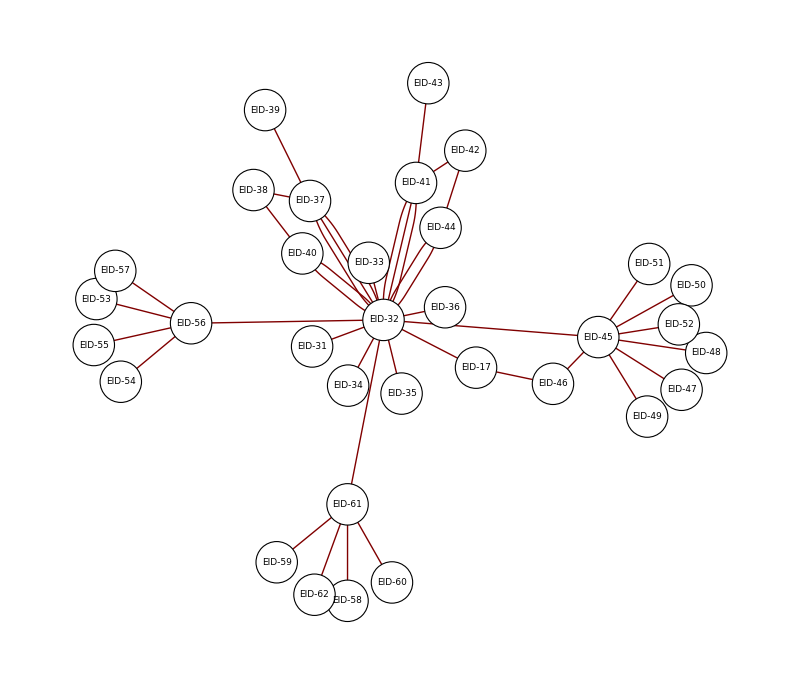

```mathematica
BokehGraph[fig]
```

```mathematica
Quit
```

```mathematica
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
fig=Figure["title"->"Vertical Bars", "tools"->All,"toolbar_location"->"right","plot_height"->350, "y_range"->fruits];fig.hbar["y"->fruits,"left"->0, "right"->{5,3,4,2,4,6},"height"->0.9, "line_color"->"red", "legend"->"A"];
```

```mathematica
fig.inspect[]
```

```mathematica
fig.show[]
```

```mathematica
fig.inspect[]
```

```mathematica
l = fig.select[LegendClass]
```

ListAttrSplat[<1>]

```mathematica
l.part[1].items.all[]
```

{LegendItem[<⋯>]}

```mathematica
tt=LegendItem["label"->value["Ulises"], "renderers"->title]
```

LegendItem[<⋯>]

```mathematica
tt.renderers.all[]
```

{Title[<⋯>]}

```mathematica
tt.tableform[]
```

attributes | BaseClass[object$7795]
Options | 
type | LegendItem
js_event_callbacks | <||>
js_property_callbacks | <||>
name | 
subscribed_events | 
tags | 
label | value[Ulises]
renderers | Bag[<1>]
$flagged | False
$Locked | False
id | EID-9

```mathematica
l.items
```

Bag[<0>]

```mathematica
Quit
```

```mathematica
Clear[fig]
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
fig=Figure["title"->"Vertical Bars", "tools"->All,"toolbar_location"->"right","plot_height"->350, "y_range"->fruits];
fig.hbar["y"->fruits,"left"->0, "right"->{5,3,4,2,4,6},"height"->0.9, "line_color"->"red"];
fig.hbar["y"->fruits,"left"->{-3,-4,-2,-4,-6,-5},"right"->0,"height"->0.9, "color"->"yellow"];
fig.ygrid."grid_line_color"=Null;
fig."x_range"."start"=-6;
fig.show[]
```

```mathematica
fig.inspect[]
```

```mathematica
BokehGraph[fig]
```

```mathematica
assoc=MBokeh`Private`getFigureJSON[fig];
```

```mathematica
MBokeh`MBokehShow[assoc,"0.12.10"]
```

```mathematica
MBokeh`MBokehWidgetShow[assoc,"0.12.16"]
```

```mathematica
Keys[assoc]
```

{id,docs,render}

```mathematica
assoc["render"]
```

{"docid":"EID-72","elementid":"EID-73","modelid":"EID-37"}

```mathematica
MBokeh`Private`$NBokehVersion
```

12.1

```mathematica
fig.inspect[]
```

```mathematica
{res.inspect[],res2.inspect[]}
```

```mathematica
Clear[fig]
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
fig=Figure["title"->"Vertical Bars", "tools"->All,"toolbar_location"->"right","plot_height"->350, "x_range"->fruits];
fig.vbar["x"->fruits,"bottom"->0,"top"->{5,3,4,2,4,6},"width"->0.9];
fig.vbar["x"->fruits,"bottom"->{-3,-4,-2,-4,-6,-5}, "top"->0,"width"->0.9,"color"->"brown"];
fig.xgrid."grid_line_color"=Null;
fig."y_range"."start"=-6;
fig.show[]
```

```mathematica
fig.show[]
```

```mathematica
fig.inspect[]
```

```mathematica
fig.vbar[0,{5,3,4,2,4,6},0.9, fruits]
```

{Figure[<⋯>],<|bottom→0,top→{5,3,4,2,4,6},width→0.9,x→{Apples,Pears,Nectarines,Plums,Grapes,Strawberries}|>}

```mathematica
fig.vbar["x"->fruits,"top"->{5,3,4,2,4,6},"width"->0.9]
```

```mathematica
fig.serializeInstances[]
```

```mathematica
fig.inspect[]
```

```mathematica
LogScale[]
```

LogScale[<⋯>]

```mathematica
fig.show[]
```

```mathematica
fig.tableform[]
```

attributes | BaseClass[object$5675]
Options | title→My Title finally working
tools→All
toolbar_location→right
plot_height→350
x_range→{Apples,Pears,Nectarines,Plums,Grapes,Strawberries}
type | Plot
above | Bag[<0>]
aspect_scale | 1
background_fill_alpha | 1.
background_fill_color | #ffffff
below | Bag[<1>]
border_fill_alpha | 1.
border_fill_color | #ffffff
extra_x_ranges | Null
extra_y_ranges | Null
hidpi | True
h_symmetry | True
left | Bag[<1>]
lod_factor | 10
lod_interval | 300
lod_threshold | 2000
lod_timeout | 500
match_aspect | False
min_border | 5
min_border_bottom | 5
min_border_left | 5
min_border_right | 5
min_border_top | 5
outline_line_alpha | 1.
outline_line_cap | butt
outline_line_color | #e5e5e5
outline_line_dash | solid
outline_line_dash_offset | 0
outline_line_join | miter
outline_line_width | 1
output_backend | canvas
plot_height | 350
plot_width | 600
renderers | Bag[<5>]
right | Bag[<0>]
subtype | Figure
title | Title[<⋯>]
title_location | above
toolbar | Toolbar[<⋯>]
toolbar_location | right
toolbar_sticky | True
v_symmetry | True
x_range | FactorRange[<⋯>]
x_scale | CategoricalScale[<⋯>]
y_range | DataRange1d[<⋯>]
y_scale | LinearScale[<⋯>]
output_filename | mbokeh.html
$flagged | True
$Locked | False
id | EID-2

```mathematica
fig."background_fill_color"="red"
```

```mathematica
fig."outline_line_color"="blue"
```

blue

```mathematica
fig.show[]
```

```mathematica
fig.references[]
```

{BasicTicker[<⋯>],BasicTicker[<⋯>],BasicTickFormatter[<⋯>],BasicTickFormatter[<⋯>],BoxAnnotation[<⋯>],BoxZoomTool[<⋯>],CrosshairTool[<⋯>],DataRange1d[<⋯>],DataRange1d[<⋯>],Figure[<⋯>],Grid[<⋯>],Grid[<⋯>],HelpTool[<⋯>],LinearAxis[<⋯>],LinearAxis[<⋯>],LinearScale[<⋯>],LinearScale[<⋯>],PanTool[<⋯>],ResetTool[<⋯>],SaveTool[<⋯>],Title[<⋯>],Toolbar[<⋯>],WheelZoomTool[<⋯>]}

```mathematica
fig.serializeJSON[]
```

```mathematica
fig.inspect[]
```

```mathematica
{fig.inspect[],InspectAttributes["bar_basic"]}
```

#### BarChart

```mathematica
Quit
```

```mathematica
refs=MBokeh`Private2`BokehBarChartReferences[{{"Apples",5},{"Pears",3},{"Nectarines",4},{"Plums",2},{"Grapes",4},{"Strawberries",6}},
ImageSize->{600,400},
 PlotLabel->"Fruit Counts","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];
breferences = Union[Sort[#["type"]&/@refs]];
{Manipulate[ExportString[MBokeh`Private`BGetTypeAttr[refs,type, All],"RawJSON", "Compact"->4],{type,breferences}], InspectAttributes["bar_basic.html"]}
```

```mathematica
json=BokehBarChartJSON[{{"Apples",5},{"Pears",3},{"Nectarines",4},{"Plums",2},{"Grapes",4},{"Strawberries",6}},
ImageSize->{600,400},
 PlotLabel->"Fruit Counts","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];MBokehShow[json]
```

```mathematica
json=BokehBarChartJSON[{{"05/15/12",5},{"05/16/12",3},{"05/17/12",4},{"Plums",2},{"Grapes",4},{"Strawberries",6}},
ImageSize->{600,400},
 PlotLabel->"Fruit Counts","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];MBokehShow[json]
```

```mathematica
data=Transpose[{dx,dy}={Range[20],RandomReal[{1,10},20]}];
json=BokehBarChartJSON[RandomReal[{1,10},20], PlotLabel->"Fruit Counts","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];MBokehShow[json]
```

#### Histogram

```mathematica
json=BokehHistogramChartJSON[RandomVariate[NormalDistribution[0,1],2000],8, PlotLabel->"Histogram","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];
MBokehShow[json]
```

#### Line

```mathematica
Quit
```

```mathematica
len=50;
json=BokehLineChartJSON[Range[len], RandomInteger[{0,10},{1,len}], PlotLabel->"Fruit Counts","Toolbar"->{"Location"->Automatic, "Tools"->{"Pan","WheelZoom","Reset","Crosshair"}}];MBokehShow[json]
```

#### Test Scatter

```mathematica
Quit
```

```mathematica
n=1000;
xdata = RandomInteger[{0,100},n];
ydata = RandomInteger[{0,100},n];
vdata = RandomReal[{0.1,1.0},n];json=BokehScatterChartJSON[xdata,ydata, vdata,PlotLabel->"Fruit Counts", "Toolbar"->{"Location"->Automatic,"Tools"->All}];
MBokehShow[json]
```

```mathematica
Quit
```

```mathematica
n=10;
xdata = RandomInteger[{0,100},n];
ydata = RandomInteger[{0,100},n];
vdata = RandomReal[{0.1,1.0},n];refs=MBokeh`Private2`BokehScatterChartReferences[xdata,ydata, vdata,PlotLabel->"Fruit Counts", "Toolbar"->{"Location"->Automatic,"Tools"->All}];
breferences = Union[Sort[#["type"]&/@refs]];
Manipulate[ExportString[MBokeh`Private`BGetTypeAttr[refs,type, All],"RawJSON", "Compact"->4],{type,breferences}]
```

```mathematica
refs=MBokeh`Private2`BokehScatterChartReferences[{{"Apples",5},{"Pears",3},{"Nectarines",4},{"Plums",2},{"Grapes",4},{"Strawberries",6}}, PlotLabel->"Fruit Counts", "Toolbar"->{"Location"->Automatic,"Tools"->All}];
breferences = Union[Sort[#["type"]&/@refs]];
Manipulate[ExportString[MBokeh`Private`BGetTypeAttr[refs,type, All],"RawJSON", "Compact"->4],{type,breferences}]
```